# Kapitola 8 - Pokrytí dat RBF sítí Demonstrace pokrytí vstupních dat složitější RBF sítí.

## Načtení knihovny NeuralNetworks

Nejdříve načteme knihovnu neuronových sítí.

```mathematica
<< NeuralNetworks`
```

Pokud pracujete v Mathematice 8.0, vypněte ještě zobrazování chybové hlášky Remove::rmnsm. Tuto hlášku vyhazují funkce knihovny NeuralNetworks. Na funkci knihovny toto nemá žádný vliv.

```mathematica
Off[Remove::rmnsm]
```

## Příprava trénovacích dat

Pokrytí dat budeme předvádět na klasifikaci do dvou tříd. Data budeme mít jednoduchá dvoudimenzionální, každá třída dat se skládá ze třech dobře oddělených shluků. Shluky se vzájemně nepřekrývají.
Vygenerujeme tyto data.

```mathematica
values=10;
cluster1x =RandomReal[{7,6},{values,1}];cluster1y=RandomReal[ {11,12},{values,1}];
cluster2x =RandomReal[{-4,-5},{values,1}];cluster2y=RandomReal[ {9,10},{values,1}];
cluster3x =RandomReal[{0,-1},{values,1}];cluster3y=RandomReal[ {12,13},{values,1}];
cluster1=Join[cluster1x,cluster1y,2];
cluster2=Join[cluster2x,cluster2y,2];
cluster3=Join[cluster3x,cluster3y,2];
inDataClass1 = Join[cluster1,cluster2,cluster3];
cluster4x =RandomReal[{2,1},{values,1}];cluster4y=RandomReal[ {4,5},{values,1}];
cluster5x =RandomReal[{-3,-4},{values,1}];cluster5y=RandomReal[ {12,13},{values,1}];
cluster6x =RandomReal[{9,8},{values,1}];cluster6y=RandomReal[ {10,9},{values,1}];
cluster4=Join[cluster4x,cluster4y,2];
cluster5=Join[cluster5x,cluster5y,2];
cluster6=Join[cluster6x,cluster6y,2];
inDataClass2 = Join[cluster4,cluster5,cluster6];
inData= Join[inDataClass1,inDataClass2];
outClass1=ConstantArray[{1,0},{3*values}];outClass2 = ConstantArray[{0,1},{3*values}];
outData= Join[outClass1,outClass2];
```

Takto vypadají naše vynerovaná vstupní data. Můžeme je chápat jako seznam bodů, které jsou určeny svými {x,y} souřadnicemi.

```mathematica
inData
```

{{6.52673,11.8053},{6.23888,11.7397},{6.34764,11.2209},{6.51405,11.6278},{6.03952,11.615},{6.96468,11.7152},{6.00908,11.4141},{6.82672,11.8782},{6.76084,11.8432},{6.59258,11.0372},{-4.47016,9.71946},{-4.94956,9.73031},{-4.59884,9.92586},{-4.63204,9.54723},{-4.1244,9.78541},{-4.37138,9.00274},{-4.30121,9.50527},{-4.53936,9.29802},{-4.8349,9.66627},{-4.79041,9.51171},{-0.931007,12.4628},{-0.130457,12.7165},{-0.0147183,12.4492},{-0.274358,12.7928},{-0.928162,12.8144},{-0.134535,12.4779},{-0.413412,12.9073},{-0.283897,12.2297},{-0.421614,12.5827},{-0.740508,12.7349},{1.21824,4.06128},{1.1397,4.44023},{1.12078,4.09764},{1.31408,4.04463},{1.22611,4.0612},{1.20231,4.96708},{1.65798,4.07116},{1.10411,4.17596},{1.82232,4.95074},{1.97657,4.77107},{-3.33104,12.4137},{-3.86495,12.9208},{-3.1852,12.2228},{-3.68869,12.6602},{-3.8348,12.8674},{-3.02201,12.5306},{-3.80621,12.3657},{-3.03336,12.8972},{-3.43367,12.5197},{-3.2533,12.9102},{8.9732,9.89003},{8.16829,9.09441},{8.91279,9.48601},{8.24695,9.40687},{8.04586,9.36576},{8.5123,9.24232},{8.60441,9.36394},{8.40605,9.21846},{8.82448,9.43652},{8.19865,9.6928}}

A takto vypadají data výstupní.

```mathematica
outData
```

{{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{0,1},{0,1},{0,1},{0,1},{0,1},{0,1},{0,1},{0,1},{0,1},{0,1},{0,1},{0,1},{0,1},{0,1},{0,1},{0,1},{0,1},{0,1},{0,1},{0,1},{0,1},{0,1},{0,1},{0,1},{0,1},{0,1},{0,1},{0,1},{0,1},{0,1}}

Vygenerovaná data si můžeme pro lepší představu zobrazit. Každá třída dat je v grafu zobrazena jinou barvou.

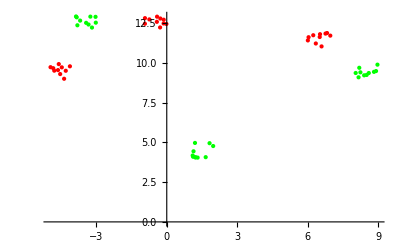

```mathematica
ListPlot[{inDataClass1,inDataClass2},PlotStyle->{Red,Green}]
```

Po vygenerování dat můžeme začít učit síť.

## Učení RBF sítě

Tato jednoduchá data budeme chtít klasifikovat pomocí RBF sítě se třemi RBF neurony, dvěma vstupy a dvěma výstupními neurony.
Vytvoříme RBF síť podle popisu výše.

```mathematica
net=InitializeRBFNet[inData,outData,3,LinearPart->False,OutputNonlinearity->Sigmoid]
```

RBFNet[{{w1, λ, w2}},{Neuron → Exp, FixedParameters → None, AccumulatedIterations → 0, CreationDate → {2011, 5, 23, 0, 20, 36.775298}, OutputNonlinearity → Sigmoid, NumberOfInputs → 2}]

Zobrazíme si informace o sítí. Tím se ujistíme že síť je opravdu taková jakou jsme popsali.

```mathematica
NetInformation[net]
```

Radial Basis Function network. Created 2011-5-23 at 0:20. The network has 2 inputs and 2 outputs.  It consists of 3 basis functions of Exp type. There is a nonlinearity at the output of type Sigmoid.

Naučíme vytvořenou síť na našich datech.

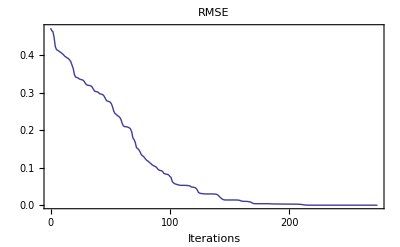

```mathematica
{net2,record}=NeuralFit[net,inData,outData,350,ReportFrequency->20];
```

## Výstup neuronové sítě

Podívejme se jak neuronová síť pokrývá jednotlivé třídy dat. Nejprve si zobrazíme výstup pro červenou třídu. Oblast grafu ohraničená červenou čarou určuje oblast dat, kterou neuronová síť klasifikuje do červené třídy. Tato oblast odpovídá datům, pro které první výstupní neuron vrací hodnotu větší než 0.5.

```mathematica
out1=Plot3D[net2[{x,y}][[1]],{x,-10,10},{y,0,30},PlotRange->All,PlotStyle->Opacity[0.2]];
inDataClass13d2=inDataClass1/.{x_?NumberQ,y_?NumberQ}:>{x,y,0};
inDataClass23d2=inDataClass2/.{x_?NumberQ,y_?NumberQ}:>{x,y,0};
data3d2=ListPointPlot3D[{inDataClass13d2,inDataClass23d2},PlotStyle->{{PointSize[Large],Red},{PointSize[Large],Green}},PlotStyle->PointSize[Large]];
out1true=Plot3D[net2[{x,y}][[1]],{x,-10,10},{y,0,30},PlotRange->All,PlotStyle->Opacity[0.7], RegionFunction->Function[{x,y,z},z>0.5],BoundaryStyle->Directive[Red,Thick]];
Show[out1,out1true,data3d2]
```

-Graphics3D-

Obdobně si zobrazíme výstup pro zelenou třídu. Oblast grafu ohraničená zelenou čarou určuje oblast dat, kterou neuronová síť klasifikuje do zelené třídy. Tato oblast odpovídá datům, pro které první výstupní neuron vrací hodnotu větší než 0.5.

```mathematica
out2true=Plot3D[net2[{x,y}][[2]],{x,-10,10},{y,0,30},PlotRange->All,PlotStyle->Opacity[0.7], RegionFunction->Function[{x,y,z},z>0.5],BoundaryStyle->Directive[Green,Thick],Mesh->None];
out2=Plot3D[net2[{x,y}][[2]],{x,-10,10},{y,0,30},PlotRange->All,PlotStyle->Opacity[0.2]];
Show[out2true,out2,data3d2]
```

-Graphics3D-

Obdobný výstup klasifikace pomocí neuronové sítě. Do 2D jsou promítnuty hraniční přímky. Po ukázání na hraniční přímku se ukáže výstup sítě ve formě vzorce.

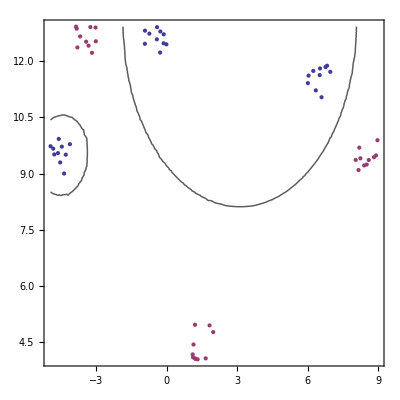

```mathematica
NetPlot[net2,inData,outData, DataFormat->Classifier]
```

## Výstup RBF neuronů

Nyní se podíváme na “vnitřnosti” neuronové sítě. Nejprve si zobrazíme výstup všech tří RBF neuronů. Abychom se dostali k výstupu RBF neuronů musíme upravit strukturu sítě obdobně jako u ukázkového příkladu sítě s jedním neuronem. Připojíme tedy každý RBF neuron přímo na výstupní neuron s vahou 1. Na výstupních neuronech se tedy zobrazí přímo výstupy z RBF neuronů.

Schéma původní sítě:   -Graphics-

Schéma upravené sítě:-Graphics-

Provedeme popsané změny.

```mathematica
net3=net2;(*nechceme si rozbít původní síť*)
net3[[1,1,3]]=Append[IdentityMatrix[3],{0,0,0}];(*nastaveni vystupni vrstvy*)
NetInformation[net3]
```

Radial Basis Function network. Created 2011-5-23 at 0:20. The network has 2 inputs and 3 outputs.  It consists of 3 basis functions of Exp type. There is a nonlinearity at the output of type Sigmoid.

A zobrazíme výstup RBF neuronů.

```mathematica
gauss1=Plot3D[net3[{x,y}][[1]],{x,-10,10},{y,0,25},PlotRange->All];
gauss2=Plot3D[net3[{x,y}][[2]],{x,-10,10},{y,0,25},PlotRange->All];
gauss3=Plot3D[net3[{x,y}][[3]],{x,-10,10},{y,0,25},PlotRange->All];
Show[gauss1,gauss2,gauss3]
```

-Graphics3D-

Výstup může mít více podob, je závislý na tom jak se neuronová síť naučila data. Pokud vidíte pouze jednu gaussovu funkci, je možné, že ostatní jsou “pod” ní. Následující průhůedné zobrazení s daty to objasní.

Přidáme do grafu ještě vstupní data pro lepší představu o jejich pokrytí (levé tlačítko myši otáčí grafem).

```mathematica
inDataClass13d=inDataClass1/.{x_?NumberQ,y_?NumberQ}:>{x,y,0.50};
inDataClass23d=inDataClass2/.{x_?NumberQ,y_?NumberQ}:>{x,y,0.50};
gauss0O=Plot3D[net3[{x,y}][[1]],{x,-10,10},{y,0,25},PlotRange->All,PlotStyle->Opacity[0.4]];
gauss1O=Plot3D[net3[{x,y}][[2]],{x,-10,10},{y,0,25},PlotRange->All,PlotStyle->Opacity[0.4]];
gauss2O=Plot3D[net3[{x,y}][[3]],{x,-10,10},{y,0,25},PlotRange->All,PlotStyle->Opacity[0.4]];
data3d=ListPointPlot3D[{inDataClass13d,inDataClass23d},PlotStyle->{{PointSize[Large],Red},{PointSize[Large],Green}},PlotStyle->PointSize[Large]];
Show[gauss0O,gauss1O,gauss2O,data3d]
```

-Graphics3D-

## Prohlášení

Tento text je vypracován jako součást bakalářské práce Adama Činčury “Demonstrační aplikace pro podporu kurzu neuronových sítí” na FEL ČVUT 2011.